## pH Titration Curve of monobasic acid

### Write a system of equations

```mathematica
sys={

(* Constants *)
10^(-Subscript[pK, a,1])==(c["H^+"]c["HZ^-"])/c["H_2Z"],
10^(-Subscript[pK, a,2])==(c["H^+"]c["Z^(2-)"])/c["HZ^-"],
10^(-Subscript[pK, w])==c["H^+"]c["OH^-"],

(* Mass balance *)
c["H_2Z"]+c["HZ^-"]+c["Z^(2-)"]==conc-c["Na^+"],
c["Na^+"]==(conc-c["Na^+"])τ,

(* Charge balance *)
c["H^+"]+c["Na^+"]==c["OH^-"]+c["HZ^-"]+2c["Z^(2-)"]

};
```

### ... and solve it

```mathematica
(* Variables elimination *)
elim=Eliminate[sys,{c["OH^-"],c["H_2Z"],c["HZ^-"],c["Z^(2-)"],c["Na^+"]}]
```

10^(-pK_w-pK_(a,1)-pK_(a,2))+10^(-pK_w-pK_(a,1)-pK_(a,2)) τ+10^(-pK_w-pK_(a,1)) c[H^+]+10^(-pK_w-pK_(a,1)) τ c[H^+]+10^-pK_w c[H^+]^2-10^(-pK_(a,1)-pK_(a,2)) c[H^+]^2+10^-pK_w τ c[H^+]^2-10^(-pK_(a,1)-pK_(a,2)) τ c[H^+]^2-10^(-pK_(a,1)) c[H^+]^3-10^(-pK_(a,1)) τ c[H^+]^3-c[H^+]^4-τ c[H^+]^4==conc c[H^+] (-2^(1-pK_(a,1)-pK_(a,2)) 5^(-pK_(a,1)-pK_(a,2))+10^(-pK_(a,1)-pK_(a,2)) τ-10^(-pK_(a,1)) c[H^+]+10^(-pK_(a,1)) τ c[H^+]+τ c[H^+]^2)

```mathematica
(* Get an analytical solution *)
sol=Solve[elim,c["H^+"]];
```

### Substitute the values of the constants and choose a solution

Numerical value of constants

```mathematica
consts=<|
Subscript[pK, a,1]->3.40,Subscript[pK, a,2]->5.20,(* malic acid *)
Subscript[pK, w]->14., (* ion-product of water at 25 °C*)
waterConc->55.35, (* at 25 °C *)
conc->1, (* acid concentration *)
c["Na^+"]-> τ (* titrant *)
|>;
```

Near the equivalence point, the machine accuracy is not enough for an accurate calculation, we explicitly set the input data precision to 100

```mathematica
consts=SetPrecision[#,100]&/@consts;
```

Substitute constant values and express pH

```mathematica
solList=-Log10[c["H^+"]]/.sol/.consts;
```

Choose an appropriate solution

```mathematica
f[τ_]=solList⟦2⟧;
```

### Plot titration curve

Calculate the points of titration curve

```mathematica
titrationCurve=Table[{τ,f[τ]},{τ,0,2.5,1/1000}];
```

Differentiate analytical analytical expression

```mathematica
df=f';
```

Calculate the points of differential curve

```mathematica
diffCurve=Table[{τ,Chop@df[τ]},{τ,0,2.5,1/1000}];
```

Plot curve

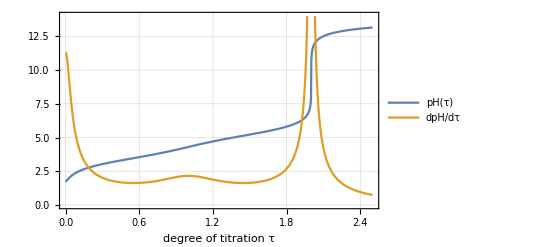

```mathematica
plot=ListLinePlot[{
titrationCurve,diffCurve
},
PlotLegends->{"pH(τ)","dpH/dτ"},
PlotRange->{{0,2.5},{0,14}},
PlotTheme->"Detailed",
FrameLabel->{"degree of titration τ"}
]
```